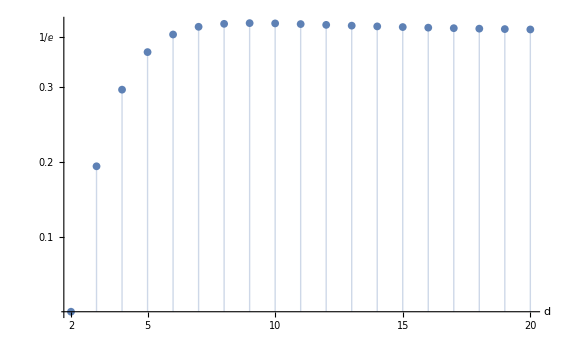

```mathematica
ListPlot[{Table[{d,(1-1/d)^(d-1)-1/2^(d-1)},{d,2,20}]},Filling->Axis,PlotRange->Full,PlotMarkers->{Automatic,8},GridLines->{{},{1/E}},AxesLabel->{"d"},Ticks->{{2,5,10,15,20},{0.1,0.2,0.3,1/E}}]
```

```mathematica
N@Table[(1-1/d)^(d-1)-1/2^(d-1),{d,2,20}]
```

```mathematica
Max@{0.,0.19444444444444445,0.296875,0.3471,0.3706275720164609,0.38094445660396603,0.38488340377807617,0.38583809312894585,0.385467364,0.38456672692953175,0.3835069493108768,0.3824525660520906,0.3814698022319634,0.3805793575160474,0.37978188823712067,0.3790700731288736,0.37843415074099485,0.3778643242952793,0.3773516951866748}
```

(1-1/d)^(d-1)-1/2^(d-1),d≥2

WolframAlphaQueryResults

```mathematica
Max@{0.,0.19444444444444445,0.296875,0.3471,0.3706275720164609,0.38094445660396603,0.38488340377807617,0.38583809312894585,0.385467364,0.38456672692953175,0.3835069493108768,0.3824525660520906,0.3814698022319634,0.3805793575160474,0.37978188823712067,0.3790700731288736,0.37843415074099485,0.3778643242952793,0.3773516951866748}
```

0.385838

```mathematica
(1-1/d)^(d-1)-1/2^(d-1)/.d->9
```

```mathematica
4251920575/11019960576-1/E
```

4251920575/11019960576-1/ⅇ

```mathematica
N@%
```

0.0179587

```mathematica
N@4/9
```

0.444444

```mathematica
N@(4251920575/11019960576)
```

0.385838

```mathematica
(1-1/d)^(d-1)-1/2^(d-1)/.d->4
```

19/64

```mathematica
N@(7/36)
```

0.194444

```mathematica
N@(1/18)
```

0.0555556

```mathematica
N[36/7]
```

5.14286

```mathematica
pvalue[n_]:=N@Abs[1/(√(2^n))(RandomInteger[1,2^n]*2-1).Table[(E^(-t 4I/(2Pi 2^n)))/(√(2^n)),{t,0,2^n-1}]]
```

```mathematica
pvalue[4]
```

0.00124707

```mathematica
test[n_,count_]:=1/count Count[Table[pvalue[n],{i,1,count}],x_/;x≤1/√(2^n)]
```

```mathematica
test[6,10000]
```

6817/10000

```mathematica
N@%
```

0.6817

```mathematica
N[1/E]
```

0.367879

```mathematica
pv2[n_]:=N@Abs[((RandomInteger[1,2^n]*2-1)/(√(2^n))).Table[1/(√(2^n)),{t,0,2^n-1}]]
```

```mathematica
test2[n_,count_]:=1/count Count[Table[pv2[n],{i,1,count}],x_/;x≤1/√(2^n)]
```

```mathematica
N@test[2,10000]
```

0.6253

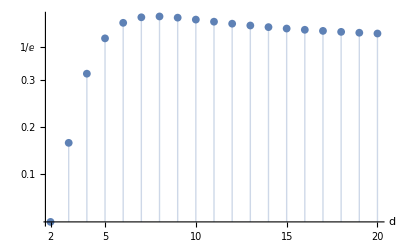

```mathematica
ListPlot[{Table[{d,(1-1/d)^(d-2)-1/2^(d-2)},{d,2,20}]},Filling->Axis,PlotRange->Full,PlotMarkers->{Automatic,8},GridLines->{{},{1/E}},AxesLabel->{"d"},Ticks->{{2,5,10,15,20},{0.1,0.2,0.3,1/E}}]
```

```mathematica
Table[{(1-1/d)^(d-2)-1/2^(d-2)},{d,2,20}]
```

{{0},{1/6},{5/16},{387/1000},{34/81},{232025/537824},{113553/262144},{263652487/612220032},{1333003/3125000},{509642052309/1207269217792},{25876958425/61917364224},{1519888982774987/3670344486987776},{1455265239705/3543369523456},{6500165227429588273/15943230000000000000},{29188527978879521/72057594037927936},{37776069439905651893775/93795878551873643905024},{380151084808422005/948746336692142592},{286506319571212647035923757/718325266223569592115396608},{104126350297911241532841/262144000000000000000000}}

```mathematica
N@{113553/262144}
```

{0.43317}